```mathematica
(*Exercise 1*)
```

```mathematica
heightInKilometers = {0, 1.525, 3.05, 4.575, 6.1}; (*These will be our x*)
airDensity = {1, 0.8617,0.7385, 0.6292,0.5328};
```

```mathematica
(*Height values (Nodes)*)
x0=0;
x1=1.525;
x2 = 3.05;
x3 =4.575;
x4 = 6.1;
```

```mathematica
(*Air density values - (Values)*)
 y0 = 1;
y1  =  0.8617;
y2 = 0.7385;
y3 =  0.6292;
y4 = 0.5328;
```

```mathematica
(*Base polynomials*)
l0[x_]= (x-x1)(x-x2)(x-x3)(x-x4)/((x0-x1)(x0-x2)(x0-x3)(x0-x4));
l1[x_] = (x-x0)(x-x2)(x-x3)(x-x4)/((x1-x0)(x1-x2)(x1-x3)(x1-x4));
l2[x_]= (x-x0)(x-x1)(x-x3)(x-x4)/((x2-x0)(x2-x1)(x2-x3)(x2-x4));
l3[x_]= (x-x0)(x-x1)(x-x2)(x-x4)/((x3-x0)(x3-x1)(x3-x2)(x3-x4));
l4[x_] = (x-x0)(x-x1)(x-x2)(x-x3)/((x4-x0)(x4-x1)(x4-x2)(x4-x3));
airDensityFunction[x_]= l0[x]y0 + l1[x]y1+l2[x]y2+l3[x]y3+l4[x]y4;
```

```mathematica
(*Plots*)
airDensityPlot= Plot[airDensityFunction[x], {x,0, 6}];
dataPointsPlot = ListPlot[{{x0, y0},{x1, y1}, {x2,y2},{x3,y3},{x4,y4}}];
```

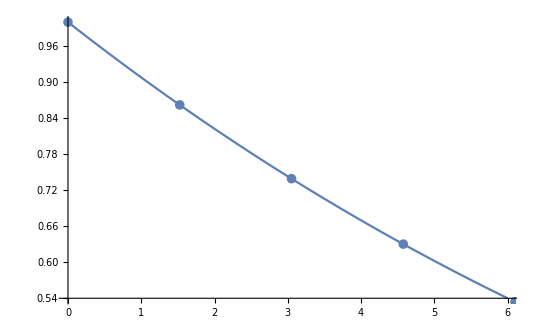
```mathematica
Show[{airDensityPlot, dataPointsPlot}]
-Graphics-
```

```mathematica
(*Air density at a height of 3km*)
airDensityFunction[3]
0.7423129331038831
```

```mathematica
(*Exercise 2*)
```

```mathematica
(*Given information*)
polyNodes =  {0, 0, 1, 1 ,2};
polyValues ={1, 0, 2,6 ,21};
coefsToFind = {a0, a1, a2, a3, a4};
```

```mathematica
(*Create the general form of the polynomial & the required derivative with undefined coeficients, we will find them in the next step*)
generalPoly[x_]  := coefsToFind[[1]]+coefsToFind[[2]]*x+coefsToFind[[3]]*x^2+coefsToFind[[4]]*x^3+coefsToFind[[5]]*x^4;
generalPolyDerivative[x_] :=generalPoly'[x];
```

```mathematica
(*Showing how the polys look, so beautiful!*)
generalPoly[x]
generalPolyDerivative[x] //N
a0+a1 x+a2 x^2+a3 x^3+a4 x^4
a1+2. a2 x+3. a3 x^2+4. a4 x^3
```

```mathematica
(*Finding the coeficients by using the Solve method. Dem bad bois hiding!*)
calcCoefs = Solve[{generalPoly[polyNodes[[1]]]==polyValues[[1]],generalPolyDerivative[polyNodes[[2]]]==polyValues[[2]],generalPoly[polyNodes[[3]]]==polyValues[[3]],generalPolyDerivative[polyNodes[[4]]]==polyValues[[4]],generalPoly[polyNodes[[5]]]==polyValues[[5]]}, coefsToFind];
```

```mathematica
(*Showing  the values we got from the solve method. We have to show them off, they are cute too!*)
calcCoefs
{{a0->1,a1->0,a2->-3,a3->4,a4->0}}
```

```mathematica
(*Substituting coeficients into the general polynomial in order to get the final answer. Almost there boiz/girlz, I can smell success*)
substitutedPoly[x_] = generalPoly[x]/.calcCoefs[[1]];
substitutedPoly[x]

(*Final result. We are da best!*)
1-3 x^2+4 x^3
```

```mathematica
(*Exercise 4*)
```

```mathematica
(*Function given in the problem description*)
f[x_]= Log[x]; 
nodes = {-1, -0.3,0.3, 1};
```

```mathematica
fourthDerivative [x_] = D[f[x], {x, 4}]
-6/x^4
```

```mathematica
(*Section 1*)
fourthDerivativeValues = fourthDerivative[nodes];
fourthDerivativeValues
{-6,-740.7407407407408,-740.7407407407408,-6}
```

Creating the R(x) polynomial based on the formula.
R[x_] = (-6/(x^4))(x+1)(x-1)(x+0.3)(x-0.3);

(Short Description)
Let 
 A = -6/(x^4) 
 B = (x+1)(x-1)(x+0.3)(x-0.3)
 In order to find the value of R(x) we want to maximize both A & B.
 
 In the interval [-1 , 1] the max value of A = -6 as we can see from Section 1 is -6.
 In the interval [-1, 1] has a max value at  0 (because it is a parabola) and the value is 0.09.
 This means that R(x ) < 1/4(0.09) <= 0.0225 for every x in the interval [-1, 1]

```mathematica
(*Exercise 6*)
```

```mathematica
DividedDiff[nodes_, values_] := (If[Length[nodes]==1,values[[1]],
(DividedDiff[nodes[[2;;Length[nodes]]],values[[2;;Length[values]]]]-DividedDiff[nodes[[1;;Length[nodes]-1]],values[[1;;Length[values]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]])]
);
```

```mathematica
Newton[power_, startNode_ ,nodeStep_, functionToInterpolate_, x_] := (
nodes = Table [startNode+i*nodeStep, {i,0,power-1}];
values = functionToInterpolate[nodes];
finalPoly = values[[1]];
For[k=2, k≤ Length[nodes], k++, finalPoly+= (DividedDiff[nodes[[1;;k]], values[[1;;k]]]*Product[(x-nodes[[i]]), {i, 1, k-1}])];
finalPoly//Expand
);
```

```mathematica
testFunction [x_]:= 1/(1+25*x^2);
NewtonPolyTest[x_] = Newton[11, -1, 0.2, testFunction, x];
nodes
values
NewtonPolyTest[x]
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

{0.0384615,0.0588235,0.1,0.2,0.5,1.,0.5,0.2,0.1,0.0588235,0.0384615}

1.+8.88178×10^-16 x-16.8552 x^2-2.13163×10^-14 x^3+123.36 x^4+1.24345×10^-13 x^5-381.434 x^6-1.7053×10^-13 x^7+494.91 x^8+5.68434×10^-14 x^9-220.942 x^10

```mathematica
funcPlot = Plot[NewtonPolyTest[x], {x,-1, 1}];
nodePlot = ListPlot[Transpose[{nodes,values}]];
```

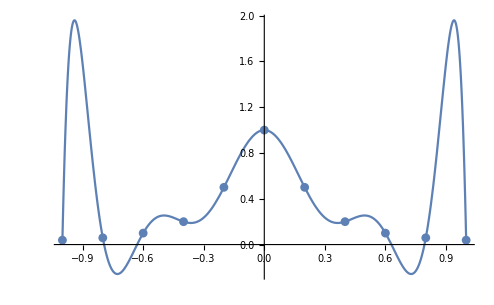

```mathematica
Show[{funcPlot,nodePlot}]
```

```mathematica
(*Exercise 7*)
```

```mathematica
LagrangeBasics[k_, nodes_, x_]:= (
basePoly=1;
For[i = 1, i ≤  Length[nodes], i++,  If[i==k, basePoly*=1 , basePoly*=  (x-nodes[[i]])/(nodes[[k]]- nodes[[i]])]];
basePoly //Expand
);

LagrangeBasics[1, {0, 1, 2}, x]
```

```mathematica
Lagrange[power_, startNode_ , nodeStep_, functionToInterpolate_, x_] := (
nodes  = Table[startNode+i*nodeStep, {i, 0, power-1}];
values = functionToInterpolate[nodes];
finalPoly = 0;
For[j = 1, j≤ Length[nodes],j++, finalPoly+= values[[j]]*LagrangeBasics[ j,nodes, x]];
finalPoly //Expand
);
```

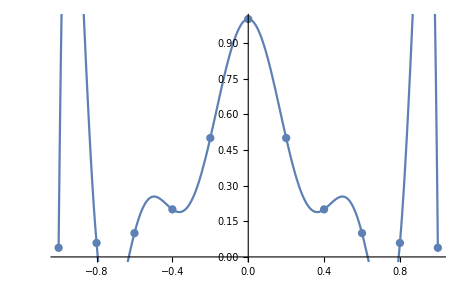
1.+2.44444×10^-15 x-16.8552 x^2+2.33502×10^-14 x^3+123.36 x^4+2.3171×10^-13 x^5-381.434 x^6-7.35273×10^-13 x^7+494.91 x^8-1.7332×10^-13 x^9-220.942 x^10
-Graphics-

```mathematica
(*Testing our creation*)
funcToInterpolate[x_]:= 1/(1+25*x^2);
lagrangeTest[x_] = Lagrange[11, -1, 0.2, funcToInterpolate,x];
lagrangeTest[x]
nodePlot = ListPlot[Transpose[{nodes,values}]];
funcPlot = Plot[lagrangeTest[x], {x,-1, 1}];
Show[{nodePlot, funcPlot}]
```

```mathematica
(*Exercise 8*)
```

```mathematica
timeInMS = {0, 1.5, 3, 4,6};
```

```mathematica
acceleration = {0, 1, 1.5, 4,2};
```

```mathematica
nodesPlot = ListPlot[Transpose[{timeInMS, acceleration}]];
```

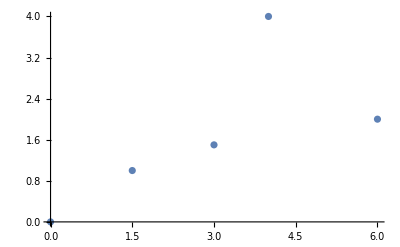

```mathematica
nodesPlot
coefs= {a1, a2,a3,a4,a5};
```

```mathematica
(*Exercise 9*)
```

```mathematica
timeInHours = Table[2i, {i, 0, 4}];
timeInHours
concentration = {0.1, 0.009,0.0011,0.00003,0.0000012};
nodesPlot = ListPlot[Transpose[{ concentration,timeInHours}]];
```

{0,2,4,6,8}

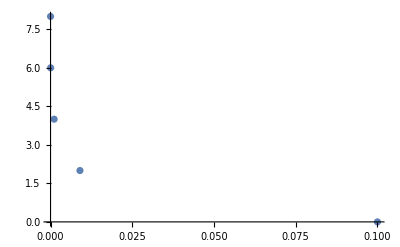

```mathematica
nodesPlot
```

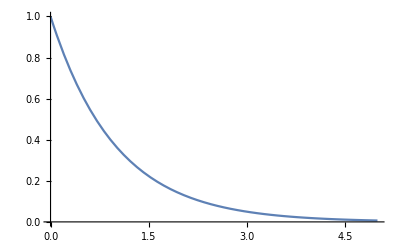

```mathematica
Plot[E^-x, {x, 0, 5}]
```

```mathematica
coefsToFind = {a1, a2, a3, a4, a5};
```

```mathematica
generalPoly[x_]:= coefsToFind[[1]]+coefsToFind[[2]]*E^(x^1) +  coefsToFind[[3]]*E^(x^2) +  coefsToFind[[4]]*E^(x^3) +  coefsToFind[[5]]*E^(x^4);
```

```mathematica
finalCoefs = Solve[{generalPoly[concentration[[1]]]==timeInHours[[1]], generalPoly[concentration[[2]]]==timeInHours[[2]]+generalPoly[concentration[[3]]]==timeInHours[[3]],generalPoly[concentration[[4]]]==timeInHours[[4]],generalPoly[concentration[[5]]]==timeInHours[[5]]}, coefsToFind];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.0001,1.001,1.01005,1.10517,1.,0.},{6.55954×10^-9,7.27669×10^-7,0.0000797933,0.00794002,0.,-2.},{1.,1.,1.,1.0011,1.,-2.},{1.,1.,1.,1.00003,1.,-6.},{1.,1.,1.,1.,1.,-8.}} may contain significant numerical errors.

```mathematica
finalCoefs
```

{{a1→-5.87193×10^10,a2→-71557.1,a3→6.79685×10^7,a4→-7.26379×10^9,a5→6.59152×10^10}}

```mathematica
finalPoly[x_] = generalPoly[x]/.finalCoefs[[1]];
```

```mathematica
finalPoly[x]
```

-5.87193×10^10-71557.1 ⅇ^x+6.79685×10^7 ⅇ^(x^2)-7.26379×10^9 ⅇ^(x^3)+6.59152×10^10 ⅇ^(x^4)

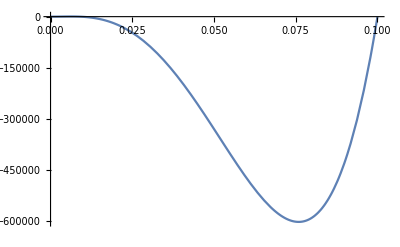

```mathematica
finalPolyPlot = Plot[finalPoly[x], {x,0.1, 0.0000012}];
finalPolyPlot
```

```mathematica
Show[{nodesPlot}]
```

-Graphics-

x0 = 1; step = 0.1; n = 5;
First way of automatically generating a list.
x0 = 1;
step = 0.1;
numberOfNodes = 5;
nodes = Table[x0+i*step,{i, 0, numberOfNodes-1}];
nodes
{1.,1.1,1.2,1.3,1.4}


Second way of automatically generating a list.
nodes2 = Range[1, 1.4, 0.1];
nodes2
{1.,1.1,1.2,1.3,1.4}